Created by Adam Kavka. I’ll be here through Spring 2014, feel free to contact me with questions: kavka.2@osu.edu

```mathematica
Needs["VectorFieldPlots`"]
```

You need to load this package (I think it’s something that worked in MAthematica 7, but works differently  in M8, so you’re  loading the old version).

General::obspkg: "VectorFieldPlots`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

Here we declare all of the points and their vectors for the launch vectors. The format is q1=ListVectorPlot3D[{{{p1x,p1y,p1z},{v1x,v1y,v1z}},{{p2x,p2y,p2z},{v2x,v2y,v2z}}...}, VectorHeads->True];
Make sure there isn’t  any scientific notation.

```mathematica
q1=ListVectorFieldPlot3D[{{{9966.53,12708.1,6.35725e+06},{5.98012,-622.549,502.391}},{{7901.43,8666.72,6.35739e+06},{519.286,332.746,509.531}},{{11300.8,12519.3,6.35698e+06},{-279.777,-537.334,522.491}},{{8579.18,7860.01,6.35824e+06},{398.37,605.072,339.395}},{{11051.5,9002.81,6.35749e+06},{-348.198,330.044,640.179}},{{11244.4,8813.43,6.35897e+06},{-557.436,531.301,216.759}},{{11516.2,11073.1,6.35707e+06},{-406.237,-284.329,627.797}},{{7318.2,8667.23,6.3586e+06},{687.273,344.216,221.747}}},VectorHeads->True];
```

This declares  the antennat point.

```mathematica
q2=ListPointPlot3D[{{9992.48,10006.6,1932.38}},PlotStyle->Red];
```

This is the receving vectors stemming from the antenna.

```mathematica
q3=ListVectorFieldPlot3D[{{{9966.53,12708.1,-251.168},{5.98012,-622.549,502.391}},{{7901.43,8666.72,-107.151},{519.286,332.746,509.531}},{{11300.8,12519.3,-518.271},{-279.777,-537.334,522.491}},{{8579.18,7860.01,742.922},{398.37,605.072,339.395}},{{11051.5,9002.81,-12.8914},{-348.198,330.044,640.179}},{{11244.4,8813.43,1467.16},{-557.436,531.301,216.759}},{{11516.2,11073.1,-431.086},{-406.237,-284.329,627.797}},{{7318.2,8667.23,1097.1},{687.273,344.216,221.747}}}, VectorHeads->True];
```

This isall of the vectors on the same plot. You’ll probably want to stretch the plot to make it more readable (stretch with a drag-click).

```mathematica
Show[q1,q2,q3]
```

-Graphics3D-

This is how to export a series of 2D plots to a pdf file called 2dvector.pdf (it’ll probably go to your home directory). readTree should generate it in the correct format. Make sure you don’t have any scientific notation, and make sure you delete the comma at the very end.

```mathematica
Export["2dvector.pdf",{Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2701.6,-2183.55},{622.578,502.391}},{{0,0},{-475.131,-366.402}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2483.51,-2039.53},{616.748,509.531}},{{0,0},{-470.662,-372.125}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2832.92,-2450.65},{605.808,522.491}},{{0,0},{-462.329,-382.429}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2570.09,-1189.46},{724.438,339.395}},{{0,0},{-552.86,-233.122}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-1459.17,-1945.27},{479.762,640.179}},{{0,0},{-366.135,-475.337}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-1729.43,-465.226},{770.075,216.759}},{{0,0},{-587.666,-121.032}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-1859.9,-2363.47},{495.854,627.797}},{{0,0},{-378.4,-465.632}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2990.95,-835.284},{768.654,221.747}},{{0,0},{-586.603,-126.085}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-1823.25,-1149.97},{676.533,426.97}},{{0,0},{-516.301,-305.669}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-1014.47,-2635.9},{285.752,747.225}},{{0,0},{-218.075,-558.966}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2861.35,-434.196},{786.24,147.736}},{{0,0},{-599.987,3.92991}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-574.337,-48.0532},{793.233,103.836}},{{0,0},{-599.813,-14.9928}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2196,-487.861},{778.198,185.494}},{{0,0},{-593.871,-85.5388}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-1236.33,-1805.17},{450.823,660.877}},{{0,0},{-344.051,-491.557}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-1452.99,-506.293},{752.826,270.653}},{{0,0},{-574.513,-173.015}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-1067.03,-832.689},{629.192,494.083}},{{0,0},{-480.173,-359.769}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2691.98,-2479.47},{587.795,542.676}},{{0,0},{-448.58,-398.467}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-1806.81,-2509.18},{468.61,648.386}},{{0,0},{-357.624,-481.773}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2754.48,-2458.85},{595.35,534.377}},{{0,0},{-454.367,-391.856}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-1559.23,-1362.3},{600.7,528.356}},{{0,0},{-458.428,-387.097}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-1548.92,-345.943},{777.452,188.596}},{{0,0},{-593.21,-90.0092}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2003.38,-2190.11},{540.64,589.668}},{{0,0},{-412.588,-435.627}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-1373.57,-1369.56},{565.963,565.407}},{{0,0},{-431.921,-416.467}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-1011.98,-2507.87},{297.733,742.533}},{{0,0},{-227.218,-555.313}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-1523.84,-2291.94},{441.495,667.145}},{{0,0},{-336.936,-496.462}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-694.274,-2237.55},{235.445,764.569}},{{0,0},{-179.682,-572.464}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2821.04,-1589.93},{697.103,392.489}},{{0,0},{-531.998,-277.449}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2628.55,-588.868},{778.722,183.28}},{{0,0},{-594.283,-82.6323}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2635.34,-2491.17},{582.102,548.778}},{{0,0},{-444.236,-403.305}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-738.913,-1016.82},{468.782,648.262}},{{0,0},{-357.755,-481.676}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2522.64,-391.45},{786.11,148.43}},{{0,0},{-599.863,-12.8059}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2814.16,-478.768},{785.054,153.918}},{{0,0},{-599.101,-32.8299}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2457.27,-1516.84},{681.065,419.703}},{{0,0},{-519.761,-299.748}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2973.98,-1059.73},{752.822,270.663}},{{0,0},{-574.521,-172.989}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-1330.45,-2067.3},{431.567,673.61}},{{0,0},{-329.363,-501.518}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2686.63,-1306.08},{718.849,351.078}},{{0,0},{-548.594,-242.99}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2018.5,-2167.43},{544.929,585.707}},{{0,0},{-415.877,-432.489}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2943.16,-2576.45},{602.426,526.386}},{{0,0},{-459.742,-385.535}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-934.325,-1218.52},{484.878,636.312}},{{0,0},{-370.04,-472.303}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-397.114,-2108.35},{149.352,785.935}},{{0,0},{-113.984,-589.074}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2753.19,-1978.02},{650.296,465.956}},{{0,0},{-496.272,-337.215}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-1525.34,-1364.28},{594.797,534.992}},{{0,0},{-453.924,-392.369}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2071.28,-383.692},{782.89,164.572}},{{0,0},{-597.404,-55.7505}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-1960.49,-1353.84},{657.815,455.279}},{{0,0},{-502.017,-328.601}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2718.19,-793.738},{766.026,230.659}},{{0,0},{-584.598,-135.075}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-824.67,-41.0222},{793.366,102.814}},{{0,0},{-599.403,26.7572}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2884.62,-596.644},{781.404,171.488}},{{0,0},{-596.329,-66.2673}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2434.58,-2032.97},{614.197,512.603}},{{0,0},{-468.719,-374.57}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-1886.33,-1988.6},{551.42,579.599}},{{0,0},{-420.819,-427.681}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2478.26,-546.708},{779.165,181.39}},{{0,0},{-594.617,-80.1915}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2905.05,-2096.34},{647.642,469.637}},{{0,0},{-494.255,-340.165}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-768.006,-2353.34},{246.992,760.917}},{{0,0},{-188.502,-569.62}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2705.47,-1575.73},{689.843,405.113}},{{0,0},{-526.459,-287.822}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-1761.52,-1542.34},{600.392,528.705}},{{0,0},{-458.195,-387.372}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2514.25,-1508.31},{684.727,413.702}},{{0,0},{-522.556,-294.848}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-1196.16,-855.14},{649.298,467.346}},{{0,0},{-495.519,-338.321}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-1541.98,-498.008},{759.316,251.871}},{{0,0},{-579.463,-155.636}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-1494.71,-797.164},{704.799,378.495}},{{0,0},{-537.872,-265.883}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-895.703,-1544.97},{402.261,691.51}},{{0,0},{-306.989,-515.517}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-819.448,-1265.74},{435.003,671.396}},{{0,0},{-331.975,-499.792}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2130.23,-580.197},{769.464,218.919}},{{0,0},{-587.218,-123.189}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2757.94,-670.865},{775.189,197.693}},{{0,0},{-591.589,-100.115}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2128.07,-1143.77},{703.851,380.255}},{{0,0},{-537.149,-267.341}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2674.07,-1059.61},{742.834,296.982}},{{0,0},{-566.899,-196.534}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-1299.44,-1940.68},{444.426,665.196}},{{0,0},{-339.165,-494.942}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-1027.65,-1151.19},{532.004,597.471}},{{0,0},{-406.005,-441.769}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2619.02,-1013.38},{745.395,290.493}},{{0,0},{-568.854,-190.8}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2214.03,-2351.49},{547.294,583.498}},{{0,0},{-417.67,-430.757}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2964.61,-1434.74},{718.664,351.458}},{{0,0},{-548.455,-243.305}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2293.14,-2510.75},{540.525,589.773}},{{0,0},{-412.509,-435.702}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2095.97,-860.442},{738.734,307.038}},{{0,0},{-563.771,-205.335}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2084.05,-494.56},{775.908,194.849}},{{0,0},{-592.125,-96.8927}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2483.27,-1138.43},{726.628,334.682}},{{0,0},{-554.532,-229.116}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-719.415,-1628.58},{321.377,732.61}},{{0,0},{-245.261,-547.583}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-1454.58,-975.658},{662.983,447.721}},{{0,0},{-505.96,-322.497}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-1469.93,-2126.46},{455.777,657.471}},{{0,0},{-347.831,-488.89}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-1714.99,-1424.69},{615.917,510.535}},{{0,0},{-470.045,-372.904}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2080.32,-2531.52},{506.928,618.89}},{{0,0},{-386.866,-458.623}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-1379.41,-1424.57},{556.804,574.43}},{{0,0},{-424.93,-423.597}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2253.89,-364.524},{785.315,152.579}},{{0,0},{-599.239,-30.2138}}},Axes->False]],Show[Plot[-2000,{x,-3000,0},Axes->False,PlotStyle->Brown],Plot[0,{x,-3000,0},Axes->False],ListVectorFieldPlot[{{{-2403.61,-639.706},{770.914,213.757}},{{0,0},{-588.327,-117.777}}},Axes->False]],}
```

2dvector.pdf

2dvector.pdf

```mathematica
?ListVectorFieldPlot
```

ListVectorFieldPlot [ { { {x_11,y_11}, {x_12,y_12}, … }, … }] generates a plot of the vector field corresponding to the array of vectors  { { {x_11,y_11}, … }, … }.
 ListVectorFieldPlot [ { {pt_1,vec_1}, {pt_2,vec_2}, … }] generates a plot of a list of vectors, each based at the corresponding point.

```mathematica
ListVectorFieldPlot[{{0,1},{2,2}},{{-1,-1},{2,2}},Axes->On]
```

ListVectorFieldPlot::lpvf: ListVectorFieldPlot requires a rectangular array of vectors or a list of {base, vector} pairs.

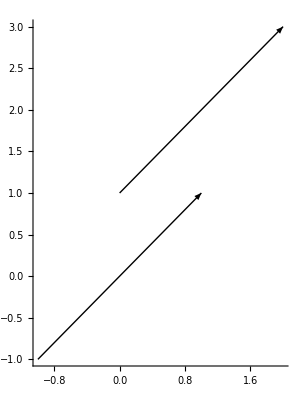

2dvector.pdf

2dvector.pdf

```mathematica
ListVectorFieldPlot[{{{0,1},{2,2}},{{-1,-1},{2,2}}},Axes->True]
```

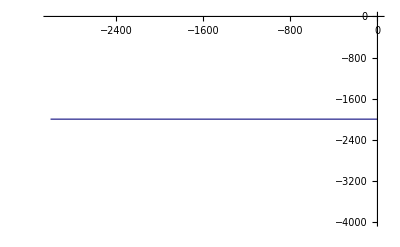

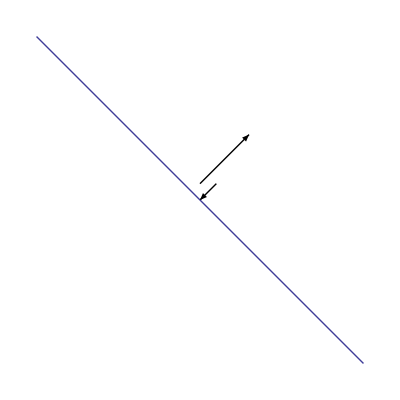

```mathematica
Show[ListVectorFieldPlot[{{{0,1},{3,3}}, {{1,1}, {-1,-1}}}], Plot[-x, {x,-10,10}]]
```

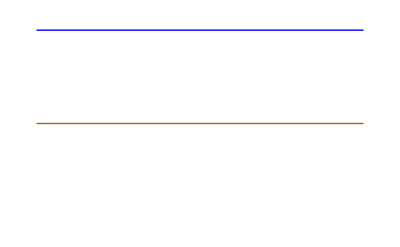

```mathematica
Show[Plot[-150,{x,-3000,0}, PlotStyle->Blue], Axes->False]
```

```mathematica
Plot[-2000, {x,-3000,0}]
```

-Graphics-

```mathematica
Export[]
```

2dvector.pdf

2dvector.pdf

```mathematica
]
```

2dvector.pdf